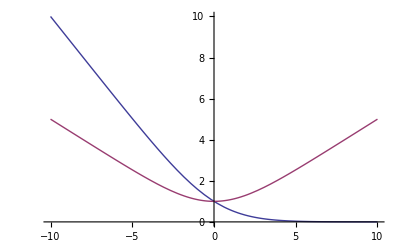

```mathematica
Plot[{t/(ⅇ^t-1),t/(ⅇ^t-1)+t/2},{t,-10,10}]
```

```mathematica
Series[t/(ⅇ^t-1),{t,0,10}]
```

1-t/2+t^2/12-t^4/720+t^6/30240-t^8/1209600+t^10/47900160+O[t]^11

```mathematica
∫_0^1 Sin[(π x)/2] x^x ⅆx//N
```

0.505975

```mathematica
f[a_,b_]:=If[a>(b-1)/2,a-b,a];
```

```mathematica
index=0;
p=37;
a=1;
n=9;
For[i=1,i≤(p-1)/2,i++,Print[f[Mod[(i^n+a i)^((p-1)/2),p],p]]]
```

-1

1

-1

1

1

1

-1

-1

1

1

1

-1

-1

-1

1

-1

-1

1

```mathematica
index=0;
p=37;
a=2;
n=9;
For[i=1,i≤p,i++,index=index+f[Mod[(i^n+a i)^((p-1)/2),p],p]]
index
N[(n-1)√p]
```

0

48.6621

```mathematica
Mod[6,7]
```

6

```mathematica
∑_(x=1)^18 x^90/37
```

2563659345837747899413921528010325150585053796899255825840461145082891991347237743391594013924010831476553585877